```mathematica
description="El -> Ga El, QED, F2(0) form factor, 1-loop";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts","FeynHelpers"};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples.The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

## Generate all desired 1-Loop diagrams using FeynArts

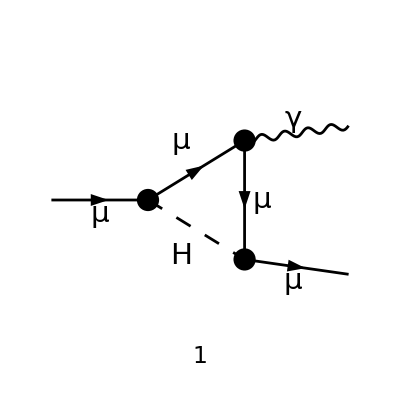

```mathematica
MakeBoxes[mu,TraditionalForm]:="μ";
MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
diags=InsertFields[CreateTopologies[1,1->2,ExcludeTopologies->{Tadpoles,WFCorrections}],{F[2,{2}]}->{V[1],F[2,{2}]},InsertionLevel->{Classes},ExcludeParticles->{S[2],S[3],V[1],V[2],V[3]}];
(*diagsCT=InsertFields[CreateCTTopologies[1,1->2,ExcludeTopologies->{Tadpoles,WFCorrections}],{F[2,{1}]}->{V[1],F[2,{1}]},InsertionLevel->{Particles},ExcludeParticles->{S[2],S[3],V[1],V[2],V[3]}];*)

Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
(*Paint[diagsCT,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];*)
```

## Convert FeynArts amplitude to FeynCalc

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags,PreFactor->1, GaugeRules->{}],IncomingMomenta->{p1},OutgoingMomenta->{k,p2},LorentzIndexNames->{mu},LoopMomenta->{q},UndoChiralSplittings->True,ChangeDimension->D,List->False,SMP->True,FinalSubstitutions->{SMP["e"]->-SMP["e"]}]/. k->p1-p2/. q->q+p1
```

-((ⅈ (ε^*)^μ(p_1-p_2) (φ(p_2,m_μ)).(ⅈ e m_μ)/(2 m_W (sin(θ_W))).(m_μ+γ·(q+p_2)).(-ⅈ e γ^μ).(m_μ+γ·(q+p_1)).(ⅈ e m_μ)/(2 m_W (sin(θ_W))).(φ(p_1,m_μ)))/((p_1+q)^2-m_μ^2).((p_2+q)^2-m_μ^2).(q^2-m_H^2))

## Fix the kinematics

```mathematica
FCClearScalarProducts[];
ME=SMP["m_mu"];
ScalarProduct[p1,p1]=ME^2;
ScalarProduct[p2,p2]=ME^2;
ScalarProduct[k,k]=0;
ScalarProduct[p1,p2]=ME^2;
```

## Amputate the photon polarisation

```mathematica
amp[1]=amp[0]//ReplaceAll[#,Pair[Momentum[Polarization[___],___],___]:>1]&//Contract//ReplaceAll[#,SMP["e"]^3->4 Pi SMP["e"] SMP["alpha_fs"]]&
```

-((ⅈ (φ(p_2,m_μ)).(ⅈ e m_μ)/(2 m_W (sin(θ_W))).(m_μ+γ·(q+p_2)).(-ⅈ e γ^μ).(m_μ+γ·(q+p_1)).(ⅈ e m_μ)/(2 m_W (sin(θ_W))).(φ(p_1,m_μ)))/((p_1+q)^2-m_μ^2).((p_2+q)^2-m_μ^2).(q^2-m_H^2))

## Perform the tensor integral decomposition in terms of Passarino-Veltman scalar integrals

```mathematica
amp[2]=TID[amp[1],q,ToPaVe->True]//DiracSimplify//Collect2[#,Spinor]&
```

1/(2 m_W^2 (sin(θ_W))^2)ⅈ π^2 e^3 m_μ^3 (p_1^μ+p_2^μ) (2 C_1(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_H^2)+C_11(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_H^2)+C_12(m_μ^2,0,m_μ^2,m_H^2,m_μ^2,m_μ^2)) (φ(p_2,m_μ)).(φ(p_1,m_μ))-1/(4 m_W^2 (sin(θ_W))^2)ⅈ π^2 e^3 m_μ^2 (B_0(0,m_μ^2,m_μ^2)+m_H^2 C_0(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_H^2)-4 m_μ^2 C_0(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_H^2)-2 C_00(0,m_μ^2,m_μ^2,m_μ^2,m_μ^2,m_H^2)) (φ(p_2,m_μ)).γ^μ.(φ(p_1,m_μ))

## Evaluate the PaVe functions using PackageX

```mathematica
amp[3]=PaXEvaluate[amp[2]]/(2 Pi)^4//Collect2[#,Spinor]&
```

(ⅈ e^3 (2 ε m_μ^4 log((π μ^2)/m_H^2)+2 ε m_H^2 m_μ^2-ε m_H^4 log(m_H^2/m_μ^2)+2 ε m_H^2 √(m_H^2 (m_H^2-4 m_μ^2)) log((√(m_H^4-4 m_H^2 m_μ^2)+m_H^2)/(2 m_H m_μ))+10 ε m_μ^4 log(m_H^2/m_μ^2)+4 ε m_μ^2 √(m_H^2 (m_H^2-4 m_μ^2)) log((√(m_H^4-4 m_H^2 m_μ^2)+m_H^2)/(2 m_H m_μ))-4 ε m_μ^4 log(μ^2/m_μ^2)+2 ε m_μ^4+2 ℽ ε m_μ^4-2 m_μ^4) (φ(p_2,m_μ)).γ^μ.(φ(p_1,m_μ)))/(256 π^2 ε m_μ^2 m_W^2 (sin(θ_W))^2)+(ⅈ e^3 (p_1^μ+p_2^μ) (-2 m_H^2 m_μ^2+m_H^4 log(m_H^2/m_μ^2)-3 m_H^2 m_μ^2 log(m_H^2/m_μ^2)-2 m_H^2 √(m_H^2 (m_H^2-4 m_μ^2)) log((√(m_H^4-4 m_H^2 m_μ^2)+m_H^2)/(2 m_H m_μ))+2 m_μ^2 √(m_H^2 (m_H^2-4 m_μ^2)) log((√(m_H^4-4 m_H^2 m_μ^2)+m_H^2)/(2 m_H m_μ))+3 m_μ^4) (φ(p_2,m_μ)).(φ(p_1,m_μ)))/(128 π^2 m_μ^3 m_W^2 (sin(θ_W))^2)

## Set D -> 4 and remove unwanted tensor structures

```mathematica
amp[4]=amp[3]//ChangeDimension[#,4]&//ReplaceAll[#,D->4]&//ReplaceAll[#,{Spinor[___].FCI[GA[mu].Spinor[___]]:>0,Spinor[___].Spinor[___]:>1,FCI[FV[p1,_]+FV[p2,_]]:>1}]&//DotSimplify//Expand//FullSimplify[#,Assumptions->{_>0}]&
```

(ⅈ e^3 (m_H^4 log(m_H^2/m_μ^2)-m_H^2 (m_μ^2 (3 log(m_H^2/m_μ^2)+2)+2 √(m_H^4-4 m_H^2 m_μ^2) log((√(m_H^4-4 m_H^2 m_μ^2)+m_H^2)/(2 m_H m_μ)))+2 m_μ^2 √(m_H^4-4 m_H^2 m_μ^2) log((√(m_H^4-4 m_H^2 m_μ^2)+m_H^2)/(2 m_H m_μ))+3 m_μ^4))/(128 π^2 m_μ^3 m_W^2 (sin(θ_W))^2)

## Rescale with Bohr magneton and evaluate numerically

```mathematica
αfs=1/126.63;(*1/128.89;*)
MW=80.385;
MZ=91.188;
mmu=105.6583745*10^-3;
ssqth=0.23153(*0.22290*)(*1-(MW/MZ)^2*);
F2=Simplify[Normal@Series[(amp[4]/((I SMP["e"])/(2 ME)))//ReplaceAll[#,{SMP["m_mu"]->x*SMP["m_H"]}]&//Expand,{x,0,4}],Assumptions->{SMP["m_H"]>0}]//FullSimplify//Simplify[#,Assumptions->{GaugeXi[Z]>0}]&//Simplify[#,Assumptions->{x>0}]&//ReplaceAll[#,{x->SMP["m_mu"]/SMP["m_H"]}]&
F2//ReplaceAll[#,{SMP["e"]->Sqrt[4 Pi αfs],SMP["alpha_fs"]->αfs,SMP["m_mu"]->mmu,SMP["m_Z"]:>MZ,SMP["m_W"]:>MW,SMP["m_H"]:>125.35,SMP["sin_W"]->Sqrt[ssqth],SMP["cos_W"]->Sqrt[1-ssqth]}]&//Expand
```

-(e^2 m_μ^4 (12 log(m_μ/m_H)+7))/(192 π^2 m_H^2 m_W^2 (sin(θ_W))^2)

2.16403×10^-14